A short-period helical wiggler as an improved source of synchrotron radiation

Brian M. Kincaid, Journal of Applied Physics 48, 2684 (1977); doi: 10.1063/1.324138
Notebook: Óscar Amaro, January 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## BESSEL FUNCTIONS K_n AND I_n

x^2ⅆ^2/ⅆSuperscriptBox[x, 2]+xⅆy/ⅆx-(x^2+α^2)y=0

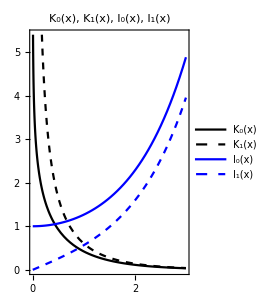

K_0'(x) = -BesselK[1,x]

∫_0^(+∞) x K_0(x)ⅆx = 1

-Graphics-

```mathematica
Clear[imgsz,pltK0,pltK1]
imgsz=200;

(*Bessel equation*)
Text["x^2ⅆ^2/ⅆSuperscriptBox[x, 2]+xⅆy/ⅆx-(x^2+α^2)y=0"]

(*Visualization*)
Plot[{BesselK[0,x],BesselK[1,x],BesselI[0,x],BesselI[1,x]},{x,0,3},AspectRatio->1.5,ImageSize->imgsz,
PlotLabel->"K_0(x), K_1(x), I_0(x), I_1(x)",PlotLegends->{"K_0(x)","K_1(x)","I_0(x)","I_1(x)"},Frame->True,
PlotStyle->{{Black},{Black,Dashed},{Blue},{Blue,Dashed}}]

(*Derivation Relation*)
Print["K_0'(x) = ",D[BesselK[0,x],x]]

(*Integration Relation*)
Print["∫_0^(+∞) x K_0(x)ⅆx = ",Integrate[x BesselK[0,x],{x,0,∞}]]

(*Small x Relations BesselK*)
pltK0=Plot[{BesselK[0,x],-Log[x]},{x,0,3},ImageSize->imgsz,
PlotLabel->"K_0(x) ~ -ln(x), x<<1",Frame->True,
PlotStyle->{Black,{Black,Dashed}},PlotRange->All,AspectRatio->1.5,PlotLegends->{"K_0(x)","-ln(x)"},PlotRange->All];

(*Small x Relations BesselI*)
pltK1=Plot[{BesselK[1,x],1/x},{x,0,3},AspectRatio->1.5,ImageSize->imgsz,
PlotLabel->"K_1(x) ~ 1/x, x<<1",PlotLegends->{"K_1(x)","1/x"},Frame->True,
PlotStyle->{Black,{Black,Dashed}}];

GraphicsRow[{pltK0,pltK1},Spacings->0]
```

## Figure 1

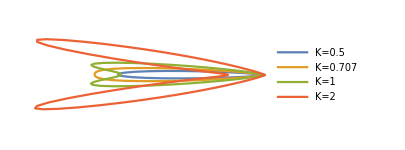

```mathematica
(* equation 24: low γ *)
Clear[γ,NN,e,ω0,c,xn,dWdΩ,K,vecθ,vecK,tab,plt1,dθ]
γ=5;NN=e=ω0=c=1.0;
xn[α_,K_,n_]:=(2 K n  α)/(1+K^2+α^2);
dWdΩ[α_,K_]:=(8 NN e^2 ω0 γ^4)/c K^2 1/((1+K^2+α^2)^3)Sum[n^2(  
N[(D[BesselJ[n,x],x]/.x->xn[α,K,n])^2+ (α/K-n/xn[α,K,n])^2 BesselJ[n,xn[α,K,n]]^2]
),{n,1,40}]

(*θ*)
dθ=0.1/5;
(*K*)
vecK={0.5,0.707,1,2};
(*dW/dΩ*)
tab=ParallelTable[N[dWdΩ[γ (θ),vecK[[i]] ]],{i,1,4,1},{θ,-π+0.01,π,dθ}];

(*view*)
max=Max[tab];
ListPolarPlot[{tab[[1]],tab[[2]],tab[[3]],tab[[4]]},Axes->False,PlotRange->{{-20 γ^2,0},{- γ^2 13,+γ^2 13}},Joined->True,ImageSize->300,PlotLegends->{"K=0.5","K=0.707","K=1","K=2"},AspectRatio->0.5]
```

## Figure 6

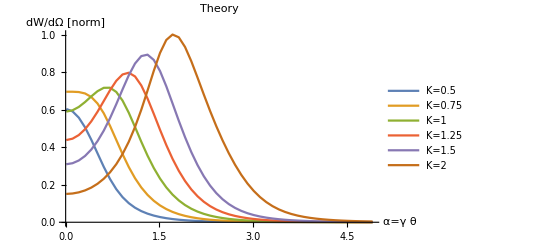

```mathematica
(* equation 24 *)
Clear[γ,NN,e,ω0,c,xn,dWdΩ,K,vecθ,vecK,tab,plt1,dα]
γ=20;NN=e=ω0=c=1.0;
xn[α_,K_,n_]:=(2 K n  α)/(1+K^2+α^2);
dWdΩ[α_,K_]:=(8 NN e^2 ω0 γ^4)/c K^2 1/((1+K^2+α^2)^3)Sum[n^2(  
N[(D[BesselJ[n,x],x]/.x->xn[α,K,n])^2+ (α/K-n/xn[α,K,n])^2 BesselJ[n,xn[α,K,n]]^2]
),{n,1,40}]

(*α*)
dα=0.1;
vecα=ParallelTable[α,{α,0.01,5,dα}];
(*K*)
vecK={0.5,0.75,1,1.25,1.5,2};
(*dW/dΩ*)
tab=ParallelTable[N[dWdΩ[α,vecK[[i]]]],{i,1,Length[vecK]},{α,0.01,5,dα}];

(*view*)
max=Max[tab];
ListPlot[{Transpose[{vecα,tab[[1]]/max}],Transpose[{vecα,tab[[2]]/max}],Transpose[{vecα,tab[[3]]/max}],Transpose[{vecα,tab[[4]]/max}],Transpose[{vecα,tab[[5]]/max}],Transpose[{vecα,tab[[6]]/max}]},PlotRange->{0,1},Joined->True,AxesLabel->{"α=γ θ","dW/dΩ [norm]"},PlotLabel->"Theory",PlotLegends->{"K=0.5","K=0.75","K=1","K=1.25","K=1.5","K=2"}]
```

## Figure 8

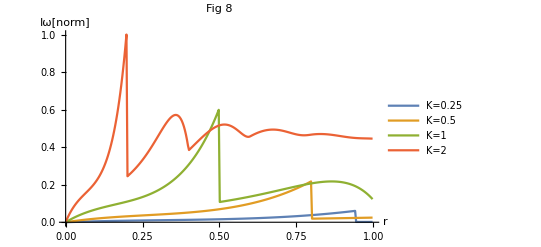

```mathematica
Clear[αn,r,K,n,xn,θ,Iω,rmin,rmax,vecr,tab,max,dr]
(*equação 25*)
αn[r_,K_,n_]:=√(n/r-1-K^2)
xn[r_,K_,n_]:=2 K r αn[r,K,n];
θ[x_]:=UnitStep[x];
Iω[r_,K_]:=r  K^2Sum[(  
(D[BesselJ[n,x],x]/.x->xn[r,K,n])^2+(αn[r,K,n]/K-n/xn[r,K,n])^2 BesselJ[n,xn[r,K,n]]^2
)θ[αn[r,K,n]^2],{n,0,30,1}]
rmin=0.001;
rmax=1.0;
dr=0.01/3;
(*r*)
vecr=ParallelTable[r,{r,rmin,rmax,dr}];
(*K*)
vecK={0.25,0.5,1.,2.};
(*dW/dΩ*)
tab=ParallelTable[Iω[r,vecK[[i]]  ],{i,1,4,1},{r,rmin,rmax,dr}]//Quiet;

(*view*)
max=Max[Chop[tab]];

ListPlot[{Transpose[{vecr,Chop[tab[[1]]/max]}],Transpose[{vecr,Chop[tab[[2]]/max]}],Transpose[{vecr,Chop[tab[[3]]/max]}],Transpose[{vecr,Chop[tab[[4]]/max]}]},PlotRange->{0,1},AxesLabel->{"r","Iω[norm]"},PlotLabel->"Fig 8",PlotLegends->{"K=0.25","K=0.5","K=1","K=2"},Joined->True]
```